```mathematica
num=200;
hbar=1;
range=10;(*Distance in fm*)
δx=range/num//N;
δk=(2π)/(num δx)//N;
space=Table[(j-(num/2))*δx+3,{j,1,num}];
kspace=Table[(j-(num/2))*δk,{j,1,num}];
absk=Table[kspace[[j]]+k0,{j,1,num}];
```

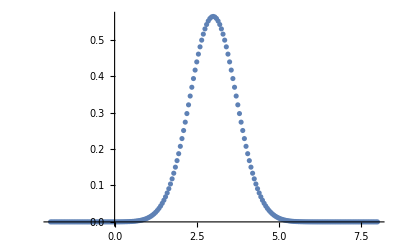

```mathematica
(*Defining the wavefunction that we are using*)
μ=1;
a=1;
V0=-.1;(*MeV*)
x0=3;
σ0=1;
k0=1;
n=(1/π)^(1/4);(*Only the case for the above conditions*)
x=.;
ψ[x_]:=n Exp[-((x-x0)^2)/(2σ0^2)]*Exp[-I k0 (x)];
ψ0=Table[ψ[space[[j]]],{j,1,num}];
ListPlot[Table[{space[[j]],ψ0[[j]]*Conjugate[ψ0[[j]]]},{j,1,num}],PlotRange->All]
```

```mathematica
x=.;
t=.;
dt=.0062;
delta= .1;
J=Length[space]-1;
dx=space[[2]]-space[[1]];
Hmax=0+1/dx^2;
τ=Hmax dt;
ii=2;
Jnτ=Table[2*(-I )^(j)BesselJ[j,τ],{j,0,10}];
Npoly=Length[Jnτ];
```

```mathematica
(*Defining the Kinetic and potential energies respectively*)
Hmax=0+(1/(dx^2));
(*We need to make it so that we have a piecewise version of this matrix for the different values of space, so for the situation were 0<=x<=a*)
potential=DiagonalMatrix[Table[0,{j,1,num}]];
For[j=1,j<=num,j++,
If[0<=space[[j]]<=a,
potential[[j,j]]=V0;
]];
kinetic=-(1/(2 dx^2))*(DiagonalMatrix[Table[-2,{j,1,num}]]+DiagonalMatrix[Table[1,{j,1,num-1}],1]+DiagonalMatrix[Table[1,{j,1,num-1}],-1]);
H=(kinetic+potential)/Hmax;
```

```mathematica
ψt=Table[Table[0,{j,1,num}],{n,1,J+1}];
ψshebyexp=Table[Table[0,{j,1,Npoly}],{n,1,J+1}];
ψt[[;;,1]]=ψ0;
ψshebyexp[[;;,1]]=ψ0;
(*Notably we have J+1 rows and NPoly columns here*)
```

```mathematica
m=num;
For[n=1,n<m-1,n++,
ψshebyexp[[;;,1]]=ψt[[;;,n]];
ψshebyexp[[;;,2]]=H.(ψshebyexp[[;;,1]]);
For[jj=3, jj<Npoly,jj++,
ψshebyexp[[;;,jj]]=2 H.ψshebyexp[[;;,jj-1]];
ψshebyexp[[;;,jj]]=ψshebyexp[[;;,jj]]-ψshebyexp[[;;,jj-2]]];
ψt[[;;,n+1]]=ψshebyexp.Jnτ]
```

```mathematica
(*Now we normalize all of our results of ψt*)
For[ib=1,ib<num,ib++,
norm=.;
norm=1/(Sqrt[Sum[ψt[[j,ib]]Conjugate[ψt[[j,ib]]],{j,1,num}]]);
 ψt[[;;,ib]]=ψt[[;;,ib]] norm;]
```

```mathematica
Sum[ψt[[j,2]]Conjugate[ψt[[j,2]]],{j,1,num}]
```

1.+0. ⅈ

```mathematica
(*Now we look to graph each of these functions*)
(**Manipulate[ListPlot[{Table[{space[[j]],ψt[[j,b]] Conjugate[ψt[[j,b]]]},{j,1,num}]},PlotRange->{{-2,8},{0,.15}}],{b,1,num,1}]
```

```mathematica
(*Now we look to animate this function to see the propogation of these functions*)
Animate[ListPlot[{Table[{space[[j]],ψt[[j,b]] Conjugate[ψt[[j,b]]]},{j,1,num}],Table[{space[[j]],potential[[j,j]]},{j,1,num}]},PlotRange->{{-1,10},{-.11,.05}},Joined->True],{b,1,num,1}]
```

```mathematica
(*These are just the Chebyshev polynomials, so now we need to incorporate the time dependence.*)
```

```mathematica
Ψ[t_]:=ψt*Exp[-I Hmax t/(2hbar)]
Ψ[t=1][[30,1]]Conjugate[Ψ[t=1][[30,1]]]
Ψ[t=100][[30,1]]Conjugate[Ψ[t=100][[30,1]]]
```

1.34986×10^-7+0. ⅈ

1.34986×10^-7+0. ⅈ

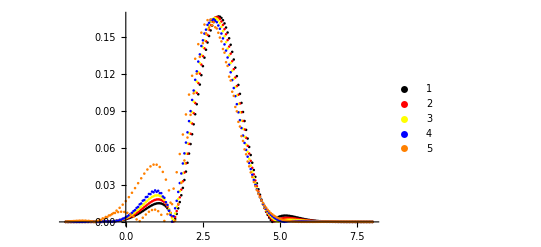

```mathematica
t=1;
ListPlot[{Table[{space[[j]],Abs[Re[Ψ[t=0][[j,10]] ]]},{j,1,num}] ,Table[{space[[j]],Abs[Re[Ψ[t=0][[j,20]]] ]},{j,1,num}] ,Table[{space[[j]],Abs[Re[Ψ[t=0][[j,30]] ]]},{j,1,num}] ,Table[{space[[j]],Abs[Re[Ψ[t=0][[j,40]]] ]},{j,1,num}] ,Table[{space[[j]],Abs[Re[Ψ[t=0][[j,50]]] ]},{j,1,num}] },PlotRange->All,PlotLegends->Automatic,PlotStyle->{Black,Red,Yellow,Blue,Orange}]
```

```mathematica
(*This correctly displays our wavefunction moving to the left.  Currently unsure why it repounds on the other side, looks to me like there is some sort of periodic boundary conditions on the situation which should not be there*)
(*Manipulate[ListPlot[{Table[{space[[j]],Re[Ψ[t=l][[j,1]] ]},{j,1,num}]},PlotRange->{{-1,11},{-0.25,0.25}}] ,{l,0,.5,.005}]
```

```mathematica
(*Animate[ListPlot[{Table[{space[[j]],Re[Ψ[t=l][[j,1]] ]},{j,1,num}]},PlotRange->{{-2,8},{-0.25,0.25}}] ,{l,0,.5,.005}]
```

```mathematica
(*Now we check for the conservation of mean energy.*)
Conjugate[ψt[[;;,10]]].H. ψt[[;;,10]]
Conjugate[ψt[[;;,20]]].H. ψt[[;;,20]]
Conjugate[ψt[[;;,30]]].H. ψt[[;;,30]]
Conjugate[ψt[[;;,40]]].H. ψt[[;;,40]]
```

0.00187318-3.11708×10^-19 ⅈ

0.00187326+9.08019×10^-19 ⅈ

0.0018741-1.6263×10^-19 ⅈ

0.0020256+6.09864×10^-20 ⅈ

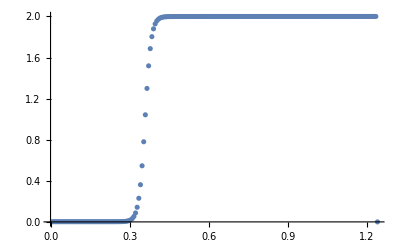

```mathematica
ListPlot[Table[{0+dt*j,Conjugate[ψt[[;;,j]]].H. ψt[[;;,j]]},{j,1,num}]]
```

```mathematica
(*Now we check for the conservation of norm here*)
Sum[Conjugate[ψt[[j,10]]] ψt[[j,10]],{j,1,num}]
Sum[Conjugate[ψt[[j,20]]] ψt[[j,20]],{j,1,num}]
Sum[Conjugate[ψt[[j,30]]] ψt[[j,30]],{j,1,num}]
Sum[Conjugate[ψt[[j,40]]]ψt[[j,40]],{j,1,num}]
```

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«1 more identical outputs»